```mathematica
ClearAll["Global`*"]
```

```mathematica
Rx[θ_]:=({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}});
Ry[θ_]:=({{Cos[θ], 0, Sin[θ]}, {0, 1, 0}, {-Sin[θ], 0, Cos[θ]}});
Rz[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
```

```mathematica
GetWx[Rmt_]:=D[Rmt,t].Transpose[Rmt];
GetW[Rmt_]:={{GetWx[Rmt][[3]][[2]]},{GetWx[Rmt][[1]][[3]]},{GetWx[Rmt][[2]][[1]]}};
```

```mathematica
(*Rotaciones al sistema de referencia de la propia esfera*)
EsfPrimRot = Rz[0];
EsfSecRot = Ry[0];
EsfTerRot = Rx[ϕsph[t]];
(*Rotaciones del cuerpo de la esfera al sistema del péndulo*)
PendSecRot = Ry[0];
PendPrimRot = Rx[βpend[t]];
```

```mathematica
REsf=EsfPrimRot.EsfSecRot.EsfTerRot;
RPend = REsf.PendPrimRot.PendSecRot;
```

```mathematica
(*Delta de posición al péndulo*)
DVecPend = RPend.{{0},{0},{-radioPendulo}};
```

```mathematica
(*Velocidad angular de O en terminos del sys de la esfera*)
ΩEsf= -GetW[Transpose[REsf]]//Simplify;
ωEsf= GetW[REsf]//Simplify;
(*Velocidad angular de O en términos del sys del péndulo*) 
ΩPend = -GetW[Transpose[RPend]]//Simplify;
ωPend= GetW[RPend]//Simplify;
```

```mathematica
(*Tensores de inercia*)
InertiaPendulo =({{IxxP, 0, 0}, {0, IyyP, 0}, {0, 0, IzzP}});
InertiaSph=({{IxxS, 0, 0}, {0, IyyS, 0}, {0, 0, IzzS}});
```

```mathematica
(*Energia rotacional de la esfera*)
EROTESF=0.5*(Transpose[ΩEsf].InertiaSph.ΩEsf)[[1]][[1]];
(*Energía rotacional del péndulo*)
EROTPEND = 0.5*(Transpose[ΩPend].InertiaPendulo.ΩPend)[[1]][[1]];
```

```mathematica
(*Posición del centro de la esfera*)
VecEsfera= {{x[t]},{y[t]},{radioEsfera}};
```

```mathematica
(*Energía cinética de la esfera*)
VelEsfera=D[VecEsfera,t];
ETRASESF=(0.5*mEsf*Transpose[VelEsfera].VelEsfera)[[1]][[1]];
(*Energía cinética del péndulo*)
VecPend = VecEsfera+DVecPend;
VelPend = D[VecPend,t];
ETRASPEND=(0.5*mPend*Transpose[VelPend].VelPend)[[1]][[1]];
```

```mathematica
(*Energías potenciales de los volantes*)
gVector=Transpose[{{0},{0},{g}}];
EPOTESF   = (mEsf*gVector.VecEsfera)[[1]][[1]];
EPOTPEND = (mPend*gVector.VecPend)[[1]][[1]];
```

```mathematica
(*Lagrangiano*)
T=EROTESF+EROTPEND+ETRASESF+ETRASPEND;
V=EPOTESF+EPOTPEND;
Lag=T-V //Chop;
```

```mathematica
(*Aplicación de las ecuaciones de Euler Lagrange, parte izquierda*)
EULA1=D[D[Lag,x'[t]],t]-D[Lag,x[t]]//Chop;
EULA2=D[D[Lag,y'[t]],t]-D[Lag,y[t]]//Chop;
EULA3=D[D[Lag,ψsph'[t]],t]-D[Lag,ψsph[t]]//Chop;
EULA4=D[D[Lag,θsph'[t]],t]-D[Lag,θsph[t]]//Chop;
EULA5=D[D[Lag,ϕsph'[t]],t]-D[Lag,ϕsph[t]]//Chop;
EULA6=D[D[Lag,αpend'[t]],t]-D[Lag,αpend[t]]//Chop;
EULA7=D[D[Lag,βpend'[t]],t]-D[Lag,βpend[t]]//Chop;
```

```mathematica
(*Restricciones*)
(*Restriccion1=(x'[t] - radioEsfera*(ωEsf[[2]][[1]]));
Restriccion2=(y'[t] + radioEsfera*(ωEsf[[1]][[1]]));*)
(*Restricciones*)
(*Restriccion1=0;
Restriccion2=0;*)
(**)
Restriccion1=0;
Restriccion2=(y'[t] + radioEsfera*(ωEsf[[1]][[1]]));
```

```mathematica
a11=D[Restriccion1,x'[t]];
a12=D[Restriccion1,y'[t]];
a13=D[Restriccion1,ψsph'[t]];
a14=D[Restriccion1,θsph'[t]];
a15=D[Restriccion1,ϕsph'[t]];
a16=D[Restriccion1,αpend'[t]];
a17=D[Restriccion1,βpend'[t]];

a21=D[Restriccion2,x'[t]];
a22=D[Restriccion2,y'[t]];
a23=D[Restriccion2,ψsph'[t]];
a24=D[Restriccion2,θsph'[t]];
a25=D[Restriccion2,ϕsph'[t]];
a26=D[Restriccion2,αpend'[t]];
a27=D[Restriccion2,βpend'[t]];
```

```mathematica
(*Restricciones*)
(*Restriccion1=(x'[t] - radioEsfera*(ωEsf[[2]][[1]]));
Restriccion2=(y'[t] + radioEsfera*(ωEsf[[1]][[1]]));*)
(*fx=-fEsfX(Restriccion1);
fy=-fEsfY(Restriccion2);
fθ=-radioEsfera Cos[ψsph[t]] *fx-radioEsfera Sin[ψsph[t]] *fy;
fϕ=-radioEsfera Cos[θsph[t]] Sin[ψsph[t]] *fx+radioEsfera Cos[θsph[t]] Cos[ψsph[t]] *fy;*)
(*Restriccion1=0;
Restriccion2=0;*)
fx=0;
fy=0;
fθ=0;
fϕ=0;
```

```mathematica
(*Fuerzas generalizadas*)
(*F1=λ1[t]*a11 +λ2[t]*a21 -fEsfXAir*x'[t]+fx;
F2=λ1[t]*a12 +λ2[t]*a22 -fEsfYAir*y'[t]+fy;
F3=λ1[t]*a13 +λ2[t]*a23-fEsfZ*ωEsf[[3]][[1]] ;
F4=λ1[t]*a14 +λ2[t]*a24 +fθ;
F5=λ1[t]*a15 +λ2[t]*a25 +fϕ;
F6=λ1[t]*a16 +λ2[t]*a26 +TorquePenduloAlfa[t]-fPendA*αpend'[t];
F7=λ1[t]*a17 +λ2[t]*a27 +TorquePenduloBeta[t]-fPendB*βpend'[t];*)
(*y haciendo TODAS las fricciones iguales a cero,en este caso,no hay rotamiento en z,ok,simplificar las fricciones del pendulo,ok,solo la friccion en y,pero es comparable a la del aire,y casi desprecialbe etc etc*)(*TorquePenduloBeta[t]=k1mot (Volt[t]-k2mot*βpend'[t]);*)

F1=λ1[t]*a11 +λ2[t]*a21 -0*x'[t]+fx;
F2=λ1[t]*a12 +λ2[t]*a22 -fEsfYAir*y'[t]+fy
F3=λ1[t]*a13 +λ2[t]*a23-0*ωEsf[[3]][[1]];
F4=λ1[t]*a14 +λ2[t]*a24 +fθ;
F5=λ1[t]*a15 +λ2[t]*a25 +fϕ
F6=λ1[t]*a16 +λ2[t]*a26 +TorquePenduloAlfa[t]-0*αpend'[t];
F7=λ1[t]*a17 +λ2[t]*a27 +TorquePenduloBeta[t]-fPendB*βpend'[t]
```

λ2[t]-fEsfYAir y'[t]

radioEsfera λ2[t]

TorquePenduloBeta[t]-fPendB βpend'[t]

```mathematica
(*Composición de ecuaciones de EULA*)
eq1=EULA1-F1;
eq2=EULA2-F2;
eq3=EULA3-F3;
eq4=EULA4-F4;
eq5=EULA5-F5;
eq6=EULA6-F6;
eq7=EULA7-F7;
(*Condición de no deslizamiento*)
eqR1=Restriccion1;
eqR2=Restriccion2;
(*Condiciones de velocidad forzada*)
eqf1=αpend'[t];
eqf2=βpend'[t]-1;
```

```mathematica
(*Eliminación de coeficiente de Lagrange de la restricción*)
(*eqs = {eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0,eqR1==0,eqR2==0,eqf1==0,eqf2==0};
eqsInit={eqs,
x[0]==0,x'[0]==0,
y[0]==0,y'[0]==0,
ψsph[0]==0,ψsph'[0]==0,
θsph[0]==0,θsph'[0]==0,
ϕsph[0]==1,ϕsph'[0]==0,
αpend[0]==0,αpend'[0]==0,
βpend[0]==-1,βpend'[0]==0}//Chop;*)
(*Eliminación de coeficiente de Lagrange de la restricción*)
(*eqs = {eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0,(*eqR1==0,eqR2==0,*)eqf1==0,eqf2==0};
eqsInit={eqs,
x[0]==0,x'[0]==0,
y[0]==0,y'[0]==0,
ψsph[0]==0,ψsph'[0]==0,
θsph[0]==0,θsph'[0]==0,
ϕsph[0]==1,ϕsph'[0]==0,
αpend[0]==0,αpend'[0]==0,
βpend[0]==-1,βpend'[0]==0}//Chop;*)
(*Es necesario poner la expresion de losmultiplicadores de lagrange para su eliminacion posterior*)eqs={eq2==0,eq5==0,eq7==0,eqR2==0,eqf2==0};
eqsInit={eqs,
y[0]==0,
y'[0]==0,
ϕsph[0]==0,
ϕsph'[0]==0,
βpend[0]==0,
βpend'[0]==0}//Chop;
(*eqs={eq2==0,eq5==0,eq7==0,(*eqR2==0,*)eqf2==0};
eqsInit={eqs,y[0]==0,y'[0]==0,ϕsph[0]==1,ϕsph'[0]==0,βpend[0]==1,βpend'[0]==0}//Chop;*)
```

```mathematica
values={
(*En el caso del péndulo, asumiremos una masa de;
m = m_v1 + m_v2 + m_mot1 + m_mot2 + m_bat + m_mecanica + m_marco;
m = 2.4 + 2.4 + 0.8 + 0.8 + 1.2 + 2 + 1 = 10.6 -> 10kg;
r = 10cm?;
Ixx = Iyy = 10 * 0.10^2 = 0.1;
Izz = 10 * 0.1^2 / 2 = 50e-3;
*)
fEsfXAir->1,
fEsfYAir->1,
fEsfZ->1,
fEsfX->1000,
fEsfY->1000,
fPendA->1,
fPendB->1,

IzzP ->50*10^-3*2,
IxxP->200*10^-3*2,
IyyP->200*10^-3*2,

(*Una esfera con masa de 2kg;
I = 2*m*r^2/3;
I = 53.333e-3 -> 50e-3
*)
IzzS ->500*10^-3*2,
IxxS ->500*10^-3*2,
IyyS ->500*10^-3*2,

mEsf->5,
mPend->5,

g->9.81,

k1mot->30/12,
k2mot->12/(216*2*Pi),

(*Parámetros*)
radioEsfera -> 0.25,
radioPendulo -> 0.15};
```

```mathematica
(*solveEqs=Eliminate[eq1==0&&eq2==0&&eq3==0&&eq4==0&&eq5==0&&eq6==0&&eq7==0&&eqR1==0&&eqR2==0,{λ1[t],λ2[t]}]*)(*solveEqs=Eliminate[eq2==0&&eq5==0&&eq7==0&&eqR2==0&&D[eqR2,t]==0,{y'[t],y''[t],λ2[t]}];*)
solveEqs=Eliminate[eq2==0&&eq5==0&&eq7==0&&eqR2==0&&D[eqR2,t]==0,{y'[t],y''[t],λ2[t]}];
```

```mathematica
solveSph=Solve[solveEqs,{ϕsph''[t],βpend''[t]}]//FullSimplify//Chop;
```

```mathematica
ϕpp=ϕsph''[t]/.solveSph[[1]][[1]]//FullSimplify;
βpp=βpend''[t]/.solveSph[[1]][[2]]//FullSimplify;
```

```mathematica
ϕppϕp=D[ϕpp,ϕsph'[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
ϕppϕ=D[ϕpp,ϕsph[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
ϕppβp=D[ϕpp,βpend'[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
ϕppβ=D[ϕpp,βpend[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
βppϕp=D[βpp,ϕsph'[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
βppϕ=D[βpp,ϕsph[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
βppβp=D[βpp,βpend'[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
βppβ=D[βpp,βpend[t]]/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
```

```mathematica
{{ϕsph''},{ϕsph'},{βpend''},{βpend'}}//MatrixForm
{{ϕsph'},{ϕsph},{βpend'},{βpend}}//MatrixForm
```

(ϕsph''
ϕsph'
βpend''
βpend')

(ϕsph'
ϕsph
βpend'
βpend)

```mathematica
SLinA=({{ϕppϕp, ϕppϕ, ϕppβp, ϕppβ}, {1, 0, 0, 0}, {βppϕp, βppϕ, βppβp, βppβ}, {0, 0, 1, 0}})//FullSimplify//Chop;
SLinA//MatrixForm
```

((fEsfYAir radioEsfera^2 (-1. IxxP-1. mPend radioPendulo^2))/(IxxP (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+mPend (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^2) | -(1. g mPend^2 radioEsfera radioPendulo^2)/(IxxP (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+mPend (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^2) | (fPendB (1. IxxP+mPend radioPendulo (-1. radioEsfera+1. radioPendulo)))/(IxxP (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+mPend (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^2) | -(1. g mPend^2 radioEsfera radioPendulo^2)/(IxxP (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+mPend (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^2)
1 | 0 | 0 | 0
(fEsfYAir radioEsfera^2 (1. IxxP^2+mPend^2 radioPendulo^3 (-1. radioEsfera+1. radioPendulo)+IxxP mPend radioPendulo (-1. radioEsfera+2. radioPendulo)))/(IxxP^2 (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+IxxP mPend (2. IxxS+(2. mEsf+1. mPend) radioEsfera^2) radioPendulo^2+mPend^2 (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^4) | (1. g mPend radioPendulo (IxxP+mPend radioPendulo^2) (-1. IxxS+radioEsfera (-1. mEsf radioEsfera-1. mPend radioEsfera+1. mPend radioPendulo)))/(IxxP^2 (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+IxxP mPend (2. IxxS+(2. mEsf+1. mPend) radioEsfera^2) radioPendulo^2+mPend^2 (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^4) | (fPendB (-1. IxxP^2+IxxP (-1. IxxS-1. mEsf radioEsfera^2-1. mPend radioEsfera^2+2. mPend radioEsfera radioPendulo-2. mPend radioPendulo^2)+mPend radioPendulo^2 (-1. IxxS-1. mEsf radioEsfera^2-1. mPend radioEsfera^2+2. mPend radioEsfera radioPendulo-1. mPend radioPendulo^2)))/(IxxP^2 (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+IxxP mPend (2. IxxS+(2. mEsf+1. mPend) radioEsfera^2) radioPendulo^2+mPend^2 (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^4) | (1. g mPend radioPendulo (IxxP+mPend radioPendulo^2) (-1. IxxS+radioEsfera (-1. mEsf radioEsfera-1. mPend radioEsfera+1. mPend radioPendulo)))/(IxxP^2 (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+IxxP mPend (2. IxxS+(2. mEsf+1. mPend) radioEsfera^2) radioPendulo^2+mPend^2 (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^4)
0 | 0 | 1 | 0)

```mathematica
uϕpp=ϕpp/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
uβpp=βpp/.{Derivative[1][ϕsph][t]->0,ϕsph[t]->0,Derivative[1][βpend][t]->0,βpend[t]->0}//Chop;
```

```mathematica
SLinB={{uϕpp},{0},{uβpp},{0}}//FullSimplify;
SLinB//MatrixForm
```

(((-1. IxxP+mPend (1. radioEsfera-1. radioPendulo) radioPendulo) TorquePenduloBeta[t])/(0.+IxxP (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+mPend (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^2)
0
((1. IxxP^2+mPend radioPendulo^2 (1. IxxS+1. mEsf radioEsfera^2+1. mPend radioEsfera^2-2. mPend radioEsfera radioPendulo+1. mPend radioPendulo^2)+IxxP (1. IxxS+1. mEsf radioEsfera^2+1. mPend radioEsfera^2-2. mPend radioEsfera radioPendulo+2. mPend radioPendulo^2)) TorquePenduloBeta[t])/(0.+IxxP^2 (1. IxxS+(1. mEsf+1. mPend) radioEsfera^2)+IxxP mPend (2. IxxS+(2. mEsf+1. mPend) radioEsfera^2) radioPendulo^2+mPend^2 (1. IxxS+1. mEsf radioEsfera^2) radioPendulo^4)
0)

```mathematica
Det[SLinA]
```

0.

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{y→InterpolatingFunction[{{0., 10.}}, <>],ϕsph→InterpolatingFunction[{{0., 10.}}, <>],βpend→InterpolatingFunction[{{0., 10.}}, <>],λ2→InterpolatingFunction[{{0., 10.}}, <>],TorquePenduloBeta→InterpolatingFunction[{{0., 10.}}, <>]}}

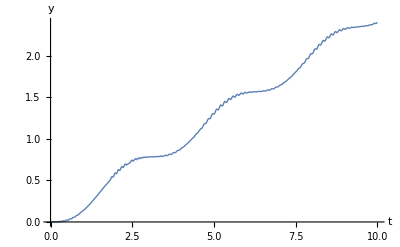

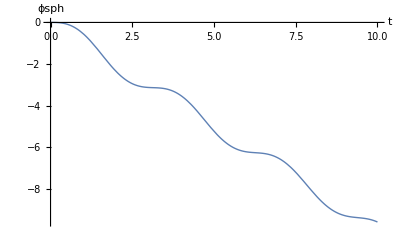

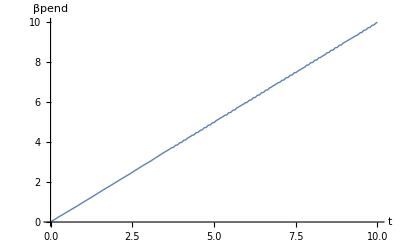

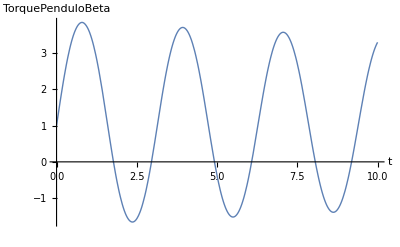

```mathematica
eqsFin= eqsInit/.values;
s=NDSolve[eqsFin,{y,ϕsph,βpend,λ2,TorquePenduloBeta},{t,0,10},Method->{"IndexReduction"->True},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->3,PrecisionGoal->3]

timeEval = 10;

(*coors=Table[{Evaluate[{x[t]}/.s][[1]][[1]],Evaluate[{y[t]}/.s][[1]][[1]]},{t,0,timeEval,0.1}];
ListPlot[coors,PlotRange->All,ImageSize->400,PlotStyle->{Thick,PointSize[Large]},BaseStyle->{20},AxesLabel->{x,y}]*)(*Plot[Evaluate[{x[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,x}]*)Plot[Evaluate[{y[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,y}]

Plot[Evaluate[{ϕsph[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,ϕsph}]
(*Plot[Evaluate[{θsph[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,θsph}] Plot[Evaluate[{ψsph[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,ψsph}] Plot[Evaluate[{αpend[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,αpend}]*)
Plot[Evaluate[{βpend[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,βpend}]

Plot[Evaluate[{TorquePenduloBeta[t]}/.s],{t,0,timeEval},PlotRange->All,ImageSize->400,PlotStyle->Thick,BaseStyle->{20},AxesLabel->{t,TorquePenduloBeta}]
```

```mathematica
(*Animate[
params=values;
(*Primer Volante de inercia*)
centroVolante1= Transpose[(VecVol1/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
directorVolante1 = Transpose[(EsfPrimRot.EsfSecRot.EsfTerRot.PendPrimRot.PendSecRot.Vol1Rot1.{{0},{0},{1}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
inicioVolante1 = (-anchoVolante * 0.5 * directorVolante1 + centroVolante1)/.params;
finVolante1 = (anchoVolante * 0.5 * directorVolante1 + centroVolante1)/.params;
Volante1=Graphics3D[{(*Green,Thick,Arrow[{centroVolante1, centroVolante1 + 10*(finVolante1- centroVolante1)}],*)FaceForm[Red],EdgeForm[Directive[Dashing[Large],Thick,Blue]],Cylinder[{inicioVolante1,finVolante1},radioVolante/.params],Axes->True}];
(*Segundo Volante de inercia*)
centroVolante2=
 Transpose[(VecVol2/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
directorVolante2 = Transpose[(EsfPrimRot.EsfSecRot.EsfTerRot.PendPrimRot.PendSecRot.Vol2Rot1.{{0},{0},{-1}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
inicioVolante2 = (-anchoVolante * 0.5 * directorVolante2 + centroVolante2)/.params;
finVolante2= (anchoVolante * 0.5 * directorVolante2 + centroVolante2)/.params;
Volante2=Graphics3D[{(*Green,Thick,Arrow[{centroVolante2, centroVolante2 + 10*(finVolante2- centroVolante2)}],*)FaceForm[Red],EdgeForm[Directive[Dashing[Large],Thick,Blue]],Cylinder[{inicioVolante2,finVolante2},radioVolante/.params],Axes->True}];
(*Péndulo de contrapeso*)
centroPendulo=Transpose[(VecPend/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
Pendulo=Graphics3D[Sphere[centroPendulo,radioVolante]]/.params;
(*Esfera de contenimiento*)
VecCentro=Transpose[(VecEsfera/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
directorEsfera=Transpose[(EsfTerRot.EsfSecRot.EsfPrimRot.{{0},{0},{.2}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
LinEsfera=Graphics3D[Arrow[{VecCentro,VecCentro+directorEsfera} ]];
Esfera=Graphics3D[{Opacity[.1],Sphere[VecCentro,radioEsfera/.params]}];

VecContacto=Transpose[(({{x[t]},{y[t]},{0}})/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
Linea=Graphics3D[Line[{{0,0,0},VecContacto}]];

(*Cilidnro del eje de la esfera*)
otroDirectorEsfera=Transpose[(EsfTerRot.EsfSecRot.EsfPrimRot.{{.2},{0},{0}}/.s[[1]][[1]]/.{t->varIter}/.s)[[1]]][[1]]/.params;
LinOtro = Graphics3D[Cylinder[{VecCentro - otroDirectorEsfera,VecCentro+otroDirectorEsfera},0.01 ]];
LinPendulo=Graphics3D[Cylinder[{VecCentro,centroPendulo},0.005 ]];
LinVolantes= Graphics3D[Cylinder[{centroVolante1,centroVolante2},0.005 ]];
Hub=Graphics3D[Sphere[VecCentro,0.02]]/.params;
Arrow1=Graphics3D[{Red,Arrow[{{0,0,0},{0,.21,0}}]}];
Arrow2=Graphics3D[{Red,Arrow[{{0,0,0},{0,-.08,0}}]}];

Show[{Arrow1,Arrow2,Hub,LinVolantes,Volante1,Volante2,Pendulo,Esfera,LinOtro(*,Linea,LinEsfera,LinOtro*),LinPendulo},PlotRange->{{-.5,.5},{-.5,.5},{0,.5}},ImageSize->900,Axes->{True,True,True},AxesLabel->{x,y,z},Boxed->False],

{varIter,0,10},AnimationRate->1,AnimationRunning->False]*)
```